Auswertung für Praktikum: Luminescence Spectroscopy
In diesem Notebook findet die Auswertung der Daten statt. Zunächst werden eine hilfreiche Funktionen definiert um Redundanzen zu vermeiden und dann wird jeder Datensatz mit individuellen Parametern gefittet.

```mathematica
(* Lade ErrorBar Package *)
Needs["ErrorBarPlots`"];

(* Setze Directory wo Messdaten liegen*)
SetDirectory["D:/doc/physik/FPR/github/lum/Praktikum_LUM/Messung/"];

(* ----------------------------------------------------------------------- *)
(* ----------------------------- Funktionen ------------------------------ *)
(* ----------------------------------------------------------------------- *)

(* importdata: Schneide Datenpunkte mit Fehler = 0 raus (Probleme bei Fit) *)
importdata[data_]:=DeleteCases[
Select[#,UnequalTo[0]]&/@Transpose[{data[[All,2]],data[[All,3]],data[[All,4]]}],
x_/;Length[x]≠3];

(* Fitmodelle model(Gauß) und model2(Doppelgauß) *)
model[ampl_,x0_,sigm_,x_]:=ampl*1/Sqrt[2*Pi*sigm^2]*Exp[-(x-x0)^2/(2 sigm^2)];
model2[ampl_,x0_,sigm_,ampl2_,x02_,sigm2_,x_]:=ampl*1/Sqrt[2*Pi*sigm^2]*Exp[-(x-x0)^2/(2 sigm^2)]+ampl2*1/Sqrt[2*Pi*sigm2^2]*Exp[-(x-x02)^2/(2 sigm2^2)];

(* f: Erstelle Fits (Gauß und Doppelgauß) mit geschätzten Peakpositionen/Amplituden *)
f[data_,x0guess_,amplguess_,x02guess_]:={
NonlinearModelFit[Transpose[{data[[All,1]],data[[All,2]]}],model[ampl,x0,sigm,x],{sigm,{x0,x0guess},{ampl,amplguess}},x,Weights->1/data[[All,3]]^2],
NonlinearModelFit[Transpose[{data[[All,1]],data[[All,2]]}],model2[ampl,x0,sigm,ampl2,x02,sigm2,x],{sigm,{x0,x0guess},{ampl,amplguess},ampl2,{x02,x02guess},sigm2},x,Weights->1/data[[All,3]]^2]
};

(* g: Zeige Fits + Datenpunkte mit Fehlerbalken *)
g[data_,list_,index_]:=Show[
ErrorListPlot[data,PlotRange->Full],Plot[list[[index]][y],{y,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Orange,PlotRange->Full]
];

(* trim: Schneide vorne und hinten Daten ab für bessere Fits *)
trim[data_,front_,back_]:=DeleteCases[data,x_/; x[[1]]<front || x[[1]]>back];
```

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

{{NonlinearModelFit[{{599.998,507.305},{600.298,502.232},{600.598,604.539},{600.899,682.044},{601.199,496.032},{601.499,744.048},{601.8,1073.15},{602.1,682.044},{602.4,729.739},{602.7,1178.08},{603.001,1178.08},{603.301,1116.07},{603.601,901.442},{603.902,1283.48},{604.202,1674.11},{604.502,2008.93},{604.802,2092.63},{605.103,2232.14},{605.403,2532.62},{605.703,3262.36},{606.004,3286.21},{606.304,3224.21},{606.604,3820.4},{606.904,4464.29},{607.205,4678.91},{607.505,4402.28},{607.805,5146.33},{608.106,5952.38},{608.406,5966.69},{608.706,5704.37},{609.006,6448.41},{609.307,7726.65},{609.607,6014.38},{609.907,7769.57},{610.208,8804.56},{610.508,9796.63},{610.808,8866.57},{611.108,10259.3},{611.409,11966.8},{611.709,12963.6},{612.009,14322.9},{612.31,17485.1},{612.61,18930.3},{612.91,22941.5},{613.21,27591.8},{613.511,31374.},{613.811,36186.5},{614.111,42596.7},{614.412,44900.4},{614.712,50037.2},{615.012,59337.8},{615.312,58550.8},{615.613,64918.2},{615.913,66964.3},{616.213,67274.3},{616.514,69072.4},{616.814,68266.4},{617.114,62585.9},{617.414,53962.1},{617.715,50595.2},{618.015,48673.1},{618.315,40178.6},{618.616,34083.1},{618.916,26847.7},{619.216,19965.3},{619.516,16440.6},{619.817,14508.9},{620.117,11656.7},{620.417,9052.58},{620.718,7726.65},{621.018,7874.5},{621.318,5151.1},{621.618,5332.34},{621.919,5022.32},{622.219,4593.06},{622.519,2666.17},{622.82,3596.23},{623.12,3176.51},{623.42,3596.23},{623.72,2728.17},{624.021,2961.88},{624.321,2120.54},{624.621,2604.17},{624.922,2914.19},{625.222,2666.17},{625.522,2294.15},{625.822,2704.33},{626.123,2356.15},{626.423,2046.13},{626.723,1922.12},{627.024,1502.4},{627.324,2232.14},{627.624,1974.59},{627.924,1426.09},{628.225,1860.12},{628.525,2189.22},{628.825,1240.08},{629.126,1488.1},{629.426,1488.1},{629.726,1416.55},{630.026,1426.09},{630.327,1330.7},{630.627,781.25},{630.927,790.551},{631.228,1060.27},{631.528,883.557},{631.828,669.643},{632.128,515.11},{632.429,496.032},{632.729,515.11},{633.029,372.024},{633.33,434.028},{633.63,686.813},{633.93,223.214},{634.23,372.024},{634.531,310.02},{634.831,372.024}},(ampl ⅇ^(-(0.515184-x0)^2/(2 sigm^2)))/(√(2 π) √(sigm^2)),{sigm,{x0,615},{ampl,70000}},0.515184,Weights→{0.0000777126,0.0000713614,0.0000711418,0.0000472932,0.0000650281,0.0000433521,0.0000434163,0.0000472932,0.0000638475,0.0000273803,0.0000273803,0.0000289014,0.0000516861,0.000027924,0.0000256901,0.0000178404,0.0000205521,0.0000160563,0.0000183967,0.0000142817,9.81556×10^-6,0.0000100043,0.0000121956,7.22534×10^-6,9.95786×10^-6,7.32711×10^-6,6.26777×10^-6,5.41901×10^-6,7.80869×10^-6,5.65462×10^-6,5.00216×10^-6,6.03004×10^-6,5.36314×10^-6,5.99673×10^-6,3.66355×10^-6,3.29256×10^-6,3.63794×10^-6,4.54145×10^-6,2.69547×10^-6,3.59406×10^-6,2.25206×10^-6,1.84477×10^-6,2.46124×10^-6,1.40601×10^-6,1.16904×10^-6,1.02811×10^-6,1.28755×10^-6,7.57241×10^-7,1.03767×10^-6,6.4464×10^-7,5.436×10^-7,7.95753×10^-7,4.96872×10^-7,6.95774×10^-7,4.7947×10^-7,4.66988×10^-7,4.72502×10^-7,7.44449×10^-7,6.6417×10^-7,8.5004×10^-7,6.62707×10^-7,8.02816×10^-7,1.36701×10^-6,1.20144×10^-6,1.6156×10^-6,2.83396×10^-6,2.22318×10^-6,2.76715×10^-6,3.56318×10^-6,6.03004×10^-6,4.09626×10^-6,9.04506×10^-6,6.04913×10^-6,6.42253×10^-6,0.000010144,0.0000120983,8.96939×10^-6,0.0000146677,8.96939×10^-6,0.0000118233,0.0000157305,0.0000169014,0.0000165151,0.0000110686,0.0000120983,0.0000140601,0.0000172287,0.0000136901,0.0000157644,0.0000167814,0.0000310116,0.0000144507,0.0000235958,0.0000226185,0.0000173408,0.0000212825,0.0000260112,0.000021676,0.000021676,0.0000328911,0.0000226185,0.0000350131,0.0000458752,0.0000544026,0.0000338028,0.000048676,0.0000535211,0.0000904506,0.0000650281,0.0000904506,0.0000867041,0.0000743178,0.000067838,0.000160563,0.000115606,0.000104045,0.0000867041}],NonlinearModelFit[{{599.998,507.305},{600.298,502.232},{600.598,604.539},{600.899,682.044},{601.199,496.032},{601.499,744.048},{601.8,1073.15},{602.1,682.044},{602.4,729.739},{602.7,1178.08},{603.001,1178.08},{603.301,1116.07},{603.601,901.442},{603.902,1283.48},{604.202,1674.11},{604.502,2008.93},{604.802,2092.63},{605.103,2232.14},{605.403,2532.62},{605.703,3262.36},{606.004,3286.21},{606.304,3224.21},{606.604,3820.4},{606.904,4464.29},{607.205,4678.91},{607.505,4402.28},{607.805,5146.33},{608.106,5952.38},{608.406,5966.69},{608.706,5704.37},{609.006,6448.41},{609.307,7726.65},{609.607,6014.38},{609.907,7769.57},{610.208,8804.56},{610.508,9796.63},{610.808,8866.57},{611.108,10259.3},{611.409,11966.8},{611.709,12963.6},{612.009,14322.9},{612.31,17485.1},{612.61,18930.3},{612.91,22941.5},{613.21,27591.8},{613.511,31374.},{613.811,36186.5},{614.111,42596.7},{614.412,44900.4},{614.712,50037.2},{615.012,59337.8},{615.312,58550.8},{615.613,64918.2},{615.913,66964.3},{616.213,67274.3},{616.514,69072.4},{616.814,68266.4},{617.114,62585.9},{617.414,53962.1},{617.715,50595.2},{618.015,48673.1},{618.315,40178.6},{618.616,34083.1},{618.916,26847.7},{619.216,19965.3},{619.516,16440.6},{619.817,14508.9},{620.117,11656.7},{620.417,9052.58},{620.718,7726.65},{621.018,7874.5},{621.318,5151.1},{621.618,5332.34},{621.919,5022.32},{622.219,4593.06},{622.519,2666.17},{622.82,3596.23},{623.12,3176.51},{623.42,3596.23},{623.72,2728.17},{624.021,2961.88},{624.321,2120.54},{624.621,2604.17},{624.922,2914.19},{625.222,2666.17},{625.522,2294.15},{625.822,2704.33},{626.123,2356.15},{626.423,2046.13},{626.723,1922.12},{627.024,1502.4},{627.324,2232.14},{627.624,1974.59},{627.924,1426.09},{628.225,1860.12},{628.525,2189.22},{628.825,1240.08},{629.126,1488.1},{629.426,1488.1},{629.726,1416.55},{630.026,1426.09},{630.327,1330.7},{630.627,781.25},{630.927,790.551},{631.228,1060.27},{631.528,883.557},{631.828,669.643},{632.128,515.11},{632.429,496.032},{632.729,515.11},{633.029,372.024},{633.33,434.028},{633.63,686.813},{633.93,223.214},{634.23,372.024},{634.531,310.02},{634.831,372.024}},(ampl ⅇ^(-(0.515184-x0)^2/(2 sigm^2)))/(√(2 π) √(sigm^2))+(ampl2 ⅇ^(-(0.515184-x02)^2/(2 sigm2^2)))/(√(2 π) √(sigm2^2)),{sigm,{x0,615},{ampl,70000},ampl2,{x02,610},sigm2},0.515184,Weights→{0.0000777126,0.0000713614,0.0000711418,0.0000472932,0.0000650281,0.0000433521,0.0000434163,0.0000472932,0.0000638475,0.0000273803,0.0000273803,0.0000289014,0.0000516861,0.000027924,0.0000256901,0.0000178404,0.0000205521,0.0000160563,0.0000183967,0.0000142817,9.81556×10^-6,0.0000100043,0.0000121956,7.22534×10^-6,9.95786×10^-6,7.32711×10^-6,6.26777×10^-6,5.41901×10^-6,7.80869×10^-6,5.65462×10^-6,5.00216×10^-6,6.03004×10^-6,5.36314×10^-6,5.99673×10^-6,3.66355×10^-6,3.29256×10^-6,3.63794×10^-6,4.54145×10^-6,2.69547×10^-6,3.59406×10^-6,2.25206×10^-6,1.84477×10^-6,2.46124×10^-6,1.40601×10^-6,1.16904×10^-6,1.02811×10^-6,1.28755×10^-6,7.57241×10^-7,1.03767×10^-6,6.4464×10^-7,5.436×10^-7,7.95753×10^-7,4.96872×10^-7,6.95774×10^-7,4.7947×10^-7,4.66988×10^-7,4.72502×10^-7,7.44449×10^-7,6.6417×10^-7,8.5004×10^-7,6.62707×10^-7,8.02816×10^-7,1.36701×10^-6,1.20144×10^-6,1.6156×10^-6,2.83396×10^-6,2.22318×10^-6,2.76715×10^-6,3.56318×10^-6,6.03004×10^-6,4.09626×10^-6,9.04506×10^-6,6.04913×10^-6,6.42253×10^-6,0.000010144,0.0000120983,8.96939×10^-6,0.0000146677,8.96939×10^-6,0.0000118233,0.0000157305,0.0000169014,0.0000165151,0.0000110686,0.0000120983,0.0000140601,0.0000172287,0.0000136901,0.0000157644,0.0000167814,0.0000310116,0.0000144507,0.0000235958,0.0000226185,0.0000173408,0.0000212825,0.0000260112,0.000021676,0.000021676,0.0000328911,0.0000226185,0.0000350131,0.0000458752,0.0000544026,0.0000338028,0.000048676,0.0000535211,0.0000904506,0.0000650281,0.0000904506,0.0000867041,0.0000743178,0.000067838,0.000160563,0.000115606,0.000104045,0.0000867041}]}}

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

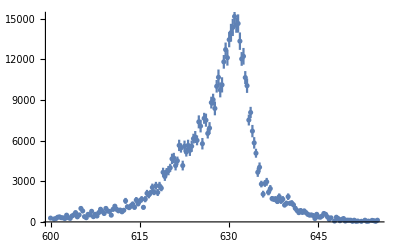

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit[{{610.208,496.032},{610.508,930.06},{610.808,1159.},{611.108,930.06},{611.409,815.591},{611.709,868.056},{612.009,744.048},{612.31,858.516},{612.61,1550.1},{612.91,1116.07},{613.21,1054.07},{613.511,1178.08},{613.811,1302.08},{614.111,1073.15},{614.412,1612.1},{614.712,1330.7},{615.012,1550.1},{615.312,1674.11},{615.613,1073.15},{615.913,1674.11},{616.213,2108.13},{616.514,1984.13},{616.814,2146.29},{617.114,2542.16},{617.414,2189.22},{617.715,2666.17},{618.015,2170.14},{618.315,2666.17},{618.616,2489.7},{618.916,3658.23},{619.216,3348.21},{619.516,3691.62},{619.817,3782.24},{620.117,3992.1},{620.417,4650.3},{620.718,4712.3},{621.018,4154.27},{621.318,4507.21},{621.618,5642.36},{621.919,5451.58},{622.219,4154.27},{622.519,5580.36},{622.82,5151.1},{623.12,5642.36},{623.42,5270.34},{623.72,5580.36},{624.021,6138.39},{624.321,6262.4},{624.621,6009.62},{624.922,7378.47},{625.222,7068.45},{625.522,5766.37},{625.822,7640.8},{626.123,7502.48},{626.423,6524.73},{626.723,6919.64},{627.024,8799.79},{627.324,9014.42},{627.624,8370.54},{627.924,10001.7},{628.225,10664.7},{628.525,9734.62},{628.825,10106.6},{629.126,11804.6},{629.426,12706.},{629.726,12109.4},{630.026,13439.4},{630.327,13950.9},{630.627,14341.5},{630.927,15152.8},{631.228,14508.9},{631.528,14632.9},{631.828,13330.9},{632.128,12019.2},{632.429,12214.8},{632.729,10645.6},{633.029,10044.6},{633.33,7512.02},{633.63,8070.05},{633.93,6696.43},{634.23,5828.37},{634.531,5065.25},{634.831,3658.23},{635.131,4030.26},{635.432,2790.18},{635.732,2046.13},{636.032,2833.1},{636.332,2957.59},{636.633,2185.64},{636.933,2455.36},{637.233,1717.03},{637.534,1674.11},{637.834,1674.11},{638.134,1502.4},{638.434,1860.12},{638.735,1550.1},{639.035,1674.11},{639.335,1244.85},{639.636,1364.09},{639.936,1860.12},{640.236,1373.63},{640.536,1395.09},{640.837,1255.58},{641.137,1004.46},{641.437,837.054},{641.738,682.044},{642.038,837.054},{642.338,697.545},{642.638,806.052},{642.939,682.044},{643.239,558.036},{643.539,496.032},{643.84,515.11},{644.14,472.184},{644.44,248.016},{644.74,558.036},{645.041,372.024},{645.341,343.407},{645.641,434.028},{645.942,620.04},{646.242,558.036},{646.542,372.024},{646.842,186.012},{647.143,300.481},{647.743,62.004},{648.044,343.407},{648.344,248.016},{648.644,85.8516},{648.944,186.012},{649.245,248.016},{649.545,62.004},{649.845,128.777}},(ampl ⅇ^(-(0.515184-x0)^2/(2 sigm^2)))/(√(2 π) √(sigm^2)),{sigm,{x0,631},{ampl,15000}},0.515184,Weights→{0.0000650281,0.0000346817,0.0000402003,0.0000346817,0.0000571267,0.0000371589,0.0000433521,0.0000542704,0.000020809,0.0000417464,0.0000306015,0.0000273803,0.0000247726,0.0000434163,0.0000200086,0.0000350131,0.000020809,0.0000192676,0.0000434163,0.0000192676,0.0000153007,0.000016257,0.0000217081,0.0000126884,0.0000212825,0.0000120983,0.0000148636,0.0000120983,0.0000187139,8.81737×10^-6,9.63379×10^-6,0.000012621,8.52827×10^-6,0.000011671,6.93633×10^-6,6.84506×10^-6,7.76455×10^-6,0.0000103372,5.71676×10^-6,8.54651×10^-6,7.76455×10^-6,5.78028×10^-6,9.04506×10^-6,5.71676×10^-6,6.12029×10^-6,5.78028×10^-6,7.59026×10^-6,5.15074×10^-6,7.75291×10^-6,4.37164×10^-6,4.56338×10^-6,5.59381×10^-6,6.09779×10^-6,4.29938×10^-6,7.14084×10^-6,5.17946×10^-6,5.29467×10^-6,5.16861×10^-6,3.85352×10^-6,4.6584×10^-6,3.02456×10^-6,3.31353×10^-6,3.19156×10^-6,3.94694×10^-6,3.66692×10^-6,2.95969×10^-6,3.20015×10^-6,2.31211×10^-6,2.49904×10^-6,3.07481×10^-6,3.21126×10^-6,2.20434×10^-6,2.41965×10^-6,3.87645×10^-6,2.64073×10^-6,4.37664×10^-6,3.56807×10^-6,6.20233×10^-6,5.77344×10^-6,4.8169×10^-6,5.53431×10^-6,9.19837×10^-6,8.81737×10^-6,8.00346×10^-6,0.0000166986,0.0000157644,0.0000164456,0.000012118,0.0000196775,0.0000145967,0.0000271352,0.000027831,0.0000192676,0.0000310116,0.0000173408,0.000020809,0.0000192676,0.0000374278,0.0000236466,0.0000173408,0.000033919,0.0000256901,0.0000342535,0.0000356807,0.0000513802,0.0000472932,0.0000428169,0.0000616563,0.0000400173,0.0000472932,0.0000578028,0.0000650281,0.0000904506,0.0000986734,0.000130056,0.0000578028,0.0000867041,0.000135676,0.0000743178,0.0000520225,0.0000834929,0.0000867041,0.000173408,0.000155058,0.000520225,0.000135676,0.000130056,0.000542704,0.000173408,0.000130056,0.000520225,0.000361802}][ParameterTable]

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit[{{610.208,496.032},{610.508,930.06},{610.808,1159.},{611.108,930.06},{611.409,815.591},{611.709,868.056},{612.009,744.048},{612.31,858.516},{612.61,1550.1},{612.91,1116.07},{613.21,1054.07},{613.511,1178.08},{613.811,1302.08},{614.111,1073.15},{614.412,1612.1},{614.712,1330.7},{615.012,1550.1},{615.312,1674.11},{615.613,1073.15},{615.913,1674.11},{616.213,2108.13},{616.514,1984.13},{616.814,2146.29},{617.114,2542.16},{617.414,2189.22},{617.715,2666.17},{618.015,2170.14},{618.315,2666.17},{618.616,2489.7},{618.916,3658.23},{619.216,3348.21},{619.516,3691.62},{619.817,3782.24},{620.117,3992.1},{620.417,4650.3},{620.718,4712.3},{621.018,4154.27},{621.318,4507.21},{621.618,5642.36},{621.919,5451.58},{622.219,4154.27},{622.519,5580.36},{622.82,5151.1},{623.12,5642.36},{623.42,5270.34},{623.72,5580.36},{624.021,6138.39},{624.321,6262.4},{624.621,6009.62},{624.922,7378.47},{625.222,7068.45},{625.522,5766.37},{625.822,7640.8},{626.123,7502.48},{626.423,6524.73},{626.723,6919.64},{627.024,8799.79},{627.324,9014.42},{627.624,8370.54},{627.924,10001.7},{628.225,10664.7},{628.525,9734.62},{628.825,10106.6},{629.126,11804.6},{629.426,12706.},{629.726,12109.4},{630.026,13439.4},{630.327,13950.9},{630.627,14341.5},{630.927,15152.8},{631.228,14508.9},{631.528,14632.9},{631.828,13330.9},{632.128,12019.2},{632.429,12214.8},{632.729,10645.6},{633.029,10044.6},{633.33,7512.02},{633.63,8070.05},{633.93,6696.43},{634.23,5828.37},{634.531,5065.25},{634.831,3658.23},{635.131,4030.26},{635.432,2790.18},{635.732,2046.13},{636.032,2833.1},{636.332,2957.59},{636.633,2185.64},{636.933,2455.36},{637.233,1717.03},{637.534,1674.11},{637.834,1674.11},{638.134,1502.4},{638.434,1860.12},{638.735,1550.1},{639.035,1674.11},{639.335,1244.85},{639.636,1364.09},{639.936,1860.12},{640.236,1373.63},{640.536,1395.09},{640.837,1255.58},{641.137,1004.46},{641.437,837.054},{641.738,682.044},{642.038,837.054},{642.338,697.545},{642.638,806.052},{642.939,682.044},{643.239,558.036},{643.539,496.032},{643.84,515.11},{644.14,472.184},{644.44,248.016},{644.74,558.036},{645.041,372.024},{645.341,343.407},{645.641,434.028},{645.942,620.04},{646.242,558.036},{646.542,372.024},{646.842,186.012},{647.143,300.481},{647.743,62.004},{648.044,343.407},{648.344,248.016},{648.644,85.8516},{648.944,186.012},{649.245,248.016},{649.545,62.004},{649.845,128.777}},(ampl ⅇ^(-(0.515184-x0)^2/(2 sigm^2)))/(√(2 π) √(sigm^2))+(ampl2 ⅇ^(-(0.515184-x02)^2/(2 sigm2^2)))/(√(2 π) √(sigm2^2)),{sigm,{x0,631},{ampl,15000},ampl2,{x02,622},sigm2},0.515184,Weights→{0.0000650281,0.0000346817,0.0000402003,0.0000346817,0.0000571267,0.0000371589,0.0000433521,0.0000542704,0.000020809,0.0000417464,0.0000306015,0.0000273803,0.0000247726,0.0000434163,0.0000200086,0.0000350131,0.000020809,0.0000192676,0.0000434163,0.0000192676,0.0000153007,0.000016257,0.0000217081,0.0000126884,0.0000212825,0.0000120983,0.0000148636,0.0000120983,0.0000187139,8.81737×10^-6,9.63379×10^-6,0.000012621,8.52827×10^-6,0.000011671,6.93633×10^-6,6.84506×10^-6,7.76455×10^-6,0.0000103372,5.71676×10^-6,8.54651×10^-6,7.76455×10^-6,5.78028×10^-6,9.04506×10^-6,5.71676×10^-6,6.12029×10^-6,5.78028×10^-6,7.59026×10^-6,5.15074×10^-6,7.75291×10^-6,4.37164×10^-6,4.56338×10^-6,5.59381×10^-6,6.09779×10^-6,4.29938×10^-6,7.14084×10^-6,5.17946×10^-6,5.29467×10^-6,5.16861×10^-6,3.85352×10^-6,4.6584×10^-6,3.02456×10^-6,3.31353×10^-6,3.19156×10^-6,3.94694×10^-6,3.66692×10^-6,2.95969×10^-6,3.20015×10^-6,2.31211×10^-6,2.49904×10^-6,3.07481×10^-6,3.21126×10^-6,2.20434×10^-6,2.41965×10^-6,3.87645×10^-6,2.64073×10^-6,4.37664×10^-6,3.56807×10^-6,6.20233×10^-6,5.77344×10^-6,4.8169×10^-6,5.53431×10^-6,9.19837×10^-6,8.81737×10^-6,8.00346×10^-6,0.0000166986,0.0000157644,0.0000164456,0.000012118,0.0000196775,0.0000145967,0.0000271352,0.000027831,0.0000192676,0.0000310116,0.0000173408,0.000020809,0.0000192676,0.0000374278,0.0000236466,0.0000173408,0.000033919,0.0000256901,0.0000342535,0.0000356807,0.0000513802,0.0000472932,0.0000428169,0.0000616563,0.0000400173,0.0000472932,0.0000578028,0.0000650281,0.0000904506,0.0000986734,0.000130056,0.0000578028,0.0000867041,0.000135676,0.0000743178,0.0000520225,0.0000834929,0.0000867041,0.000173408,0.000155058,0.000520225,0.000135676,0.000130056,0.000542704,0.000173408,0.000130056,0.000520225,0.000361802}][ParameterTable]

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit[{{610.208,496.032},{610.508,930.06},{610.808,1159.},{611.108,930.06},{611.409,815.591},{611.709,868.056},{612.009,744.048},{612.31,858.516},{612.61,1550.1},{612.91,1116.07},{613.21,1054.07},{613.511,1178.08},{613.811,1302.08},{614.111,1073.15},{614.412,1612.1},{614.712,1330.7},{615.012,1550.1},{615.312,1674.11},{615.613,1073.15},{615.913,1674.11},{616.213,2108.13},{616.514,1984.13},{616.814,2146.29},{617.114,2542.16},{617.414,2189.22},{617.715,2666.17},{618.015,2170.14},{618.315,2666.17},{618.616,2489.7},{618.916,3658.23},{619.216,3348.21},{619.516,3691.62},{619.817,3782.24},{620.117,3992.1},{620.417,4650.3},{620.718,4712.3},{621.018,4154.27},{621.318,4507.21},{621.618,5642.36},{621.919,5451.58},{622.219,4154.27},{622.519,5580.36},{622.82,5151.1},{623.12,5642.36},{623.42,5270.34},{623.72,5580.36},{624.021,6138.39},{624.321,6262.4},{624.621,6009.62},{624.922,7378.47},{625.222,7068.45},{625.522,5766.37},{625.822,7640.8},{626.123,7502.48},{626.423,6524.73},{626.723,6919.64},{627.024,8799.79},{627.324,9014.42},{627.624,8370.54},{627.924,10001.7},{628.225,10664.7},{628.525,9734.62},{628.825,10106.6},{629.126,11804.6},{629.426,12706.},{629.726,12109.4},{630.026,13439.4},{630.327,13950.9},{630.627,14341.5},{630.927,15152.8},{631.228,14508.9},{631.528,14632.9},{631.828,13330.9},{632.128,12019.2},{632.429,12214.8},{632.729,10645.6},{633.029,10044.6},{633.33,7512.02},{633.63,8070.05},{633.93,6696.43},{634.23,5828.37},{634.531,5065.25},{634.831,3658.23},{635.131,4030.26},{635.432,2790.18},{635.732,2046.13},{636.032,2833.1},{636.332,2957.59},{636.633,2185.64},{636.933,2455.36},{637.233,1717.03},{637.534,1674.11},{637.834,1674.11},{638.134,1502.4},{638.434,1860.12},{638.735,1550.1},{639.035,1674.11},{639.335,1244.85},{639.636,1364.09},{639.936,1860.12},{640.236,1373.63},{640.536,1395.09},{640.837,1255.58},{641.137,1004.46},{641.437,837.054},{641.738,682.044},{642.038,837.054},{642.338,697.545},{642.638,806.052},{642.939,682.044},{643.239,558.036},{643.539,496.032},{643.84,515.11},{644.14,472.184},{644.44,248.016},{644.74,558.036},{645.041,372.024},{645.341,343.407},{645.641,434.028},{645.942,620.04},{646.242,558.036},{646.542,372.024},{646.842,186.012},{647.143,300.481},{647.743,62.004},{648.044,343.407},{648.344,248.016},{648.644,85.8516},{648.944,186.012},{649.245,248.016},{649.545,62.004},{649.845,128.777}},(ampl ⅇ^(-(0.515184-x0)^2/(2 sigm^2)))/(√(2 π) √(sigm^2)),{sigm,{x0,631},{ampl,15000}},0.515184,Weights→{0.0000650281,0.0000346817,0.0000402003,0.0000346817,0.0000571267,0.0000371589,0.0000433521,0.0000542704,0.000020809,0.0000417464,0.0000306015,0.0000273803,0.0000247726,0.0000434163,0.0000200086,0.0000350131,0.000020809,0.0000192676,0.0000434163,0.0000192676,0.0000153007,0.000016257,0.0000217081,0.0000126884,0.0000212825,0.0000120983,0.0000148636,0.0000120983,0.0000187139,8.81737×10^-6,9.63379×10^-6,0.000012621,8.52827×10^-6,0.000011671,6.93633×10^-6,6.84506×10^-6,7.76455×10^-6,0.0000103372,5.71676×10^-6,8.54651×10^-6,7.76455×10^-6,5.78028×10^-6,9.04506×10^-6,5.71676×10^-6,6.12029×10^-6,5.78028×10^-6,7.59026×10^-6,5.15074×10^-6,7.75291×10^-6,4.37164×10^-6,4.56338×10^-6,5.59381×10^-6,6.09779×10^-6,4.29938×10^-6,7.14084×10^-6,5.17946×10^-6,5.29467×10^-6,5.16861×10^-6,3.85352×10^-6,4.6584×10^-6,3.02456×10^-6,3.31353×10^-6,3.19156×10^-6,3.94694×10^-6,3.66692×10^-6,2.95969×10^-6,3.20015×10^-6,2.31211×10^-6,2.49904×10^-6,3.07481×10^-6,3.21126×10^-6,2.20434×10^-6,2.41965×10^-6,3.87645×10^-6,2.64073×10^-6,4.37664×10^-6,3.56807×10^-6,6.20233×10^-6,5.77344×10^-6,4.8169×10^-6,5.53431×10^-6,9.19837×10^-6,8.81737×10^-6,8.00346×10^-6,0.0000166986,0.0000157644,0.0000164456,0.000012118,0.0000196775,0.0000145967,0.0000271352,0.000027831,0.0000192676,0.0000310116,0.0000173408,0.000020809,0.0000192676,0.0000374278,0.0000236466,0.0000173408,0.000033919,0.0000256901,0.0000342535,0.0000356807,0.0000513802,0.0000472932,0.0000428169,0.0000616563,0.0000400173,0.0000472932,0.0000578028,0.0000650281,0.0000904506,0.0000986734,0.000130056,0.0000578028,0.0000867041,0.000135676,0.0000743178,0.0000520225,0.0000834929,0.0000867041,0.000173408,0.000155058,0.000520225,0.000135676,0.000130056,0.000542704,0.000173408,0.000130056,0.000520225,0.000361802}][AdjustedRSquared]

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit[{{610.208,496.032},{610.508,930.06},{610.808,1159.},{611.108,930.06},{611.409,815.591},{611.709,868.056},{612.009,744.048},{612.31,858.516},{612.61,1550.1},{612.91,1116.07},{613.21,1054.07},{613.511,1178.08},{613.811,1302.08},{614.111,1073.15},{614.412,1612.1},{614.712,1330.7},{615.012,1550.1},{615.312,1674.11},{615.613,1073.15},{615.913,1674.11},{616.213,2108.13},{616.514,1984.13},{616.814,2146.29},{617.114,2542.16},{617.414,2189.22},{617.715,2666.17},{618.015,2170.14},{618.315,2666.17},{618.616,2489.7},{618.916,3658.23},{619.216,3348.21},{619.516,3691.62},{619.817,3782.24},{620.117,3992.1},{620.417,4650.3},{620.718,4712.3},{621.018,4154.27},{621.318,4507.21},{621.618,5642.36},{621.919,5451.58},{622.219,4154.27},{622.519,5580.36},{622.82,5151.1},{623.12,5642.36},{623.42,5270.34},{623.72,5580.36},{624.021,6138.39},{624.321,6262.4},{624.621,6009.62},{624.922,7378.47},{625.222,7068.45},{625.522,5766.37},{625.822,7640.8},{626.123,7502.48},{626.423,6524.73},{626.723,6919.64},{627.024,8799.79},{627.324,9014.42},{627.624,8370.54},{627.924,10001.7},{628.225,10664.7},{628.525,9734.62},{628.825,10106.6},{629.126,11804.6},{629.426,12706.},{629.726,12109.4},{630.026,13439.4},{630.327,13950.9},{630.627,14341.5},{630.927,15152.8},{631.228,14508.9},{631.528,14632.9},{631.828,13330.9},{632.128,12019.2},{632.429,12214.8},{632.729,10645.6},{633.029,10044.6},{633.33,7512.02},{633.63,8070.05},{633.93,6696.43},{634.23,5828.37},{634.531,5065.25},{634.831,3658.23},{635.131,4030.26},{635.432,2790.18},{635.732,2046.13},{636.032,2833.1},{636.332,2957.59},{636.633,2185.64},{636.933,2455.36},{637.233,1717.03},{637.534,1674.11},{637.834,1674.11},{638.134,1502.4},{638.434,1860.12},{638.735,1550.1},{639.035,1674.11},{639.335,1244.85},{639.636,1364.09},{639.936,1860.12},{640.236,1373.63},{640.536,1395.09},{640.837,1255.58},{641.137,1004.46},{641.437,837.054},{641.738,682.044},{642.038,837.054},{642.338,697.545},{642.638,806.052},{642.939,682.044},{643.239,558.036},{643.539,496.032},{643.84,515.11},{644.14,472.184},{644.44,248.016},{644.74,558.036},{645.041,372.024},{645.341,343.407},{645.641,434.028},{645.942,620.04},{646.242,558.036},{646.542,372.024},{646.842,186.012},{647.143,300.481},{647.743,62.004},{648.044,343.407},{648.344,248.016},{648.644,85.8516},{648.944,186.012},{649.245,248.016},{649.545,62.004},{649.845,128.777}},(ampl ⅇ^(-(0.515184-x0)^2/(2 sigm^2)))/(√(2 π) √(sigm^2))+(ampl2 ⅇ^(-(0.515184-x02)^2/(2 sigm2^2)))/(√(2 π) √(sigm2^2)),{sigm,{x0,631},{ampl,15000},ampl2,{x02,622},sigm2},0.515184,Weights→{0.0000650281,0.0000346817,0.0000402003,0.0000346817,0.0000571267,0.0000371589,0.0000433521,0.0000542704,0.000020809,0.0000417464,0.0000306015,0.0000273803,0.0000247726,0.0000434163,0.0000200086,0.0000350131,0.000020809,0.0000192676,0.0000434163,0.0000192676,0.0000153007,0.000016257,0.0000217081,0.0000126884,0.0000212825,0.0000120983,0.0000148636,0.0000120983,0.0000187139,8.81737×10^-6,9.63379×10^-6,0.000012621,8.52827×10^-6,0.000011671,6.93633×10^-6,6.84506×10^-6,7.76455×10^-6,0.0000103372,5.71676×10^-6,8.54651×10^-6,7.76455×10^-6,5.78028×10^-6,9.04506×10^-6,5.71676×10^-6,6.12029×10^-6,5.78028×10^-6,7.59026×10^-6,5.15074×10^-6,7.75291×10^-6,4.37164×10^-6,4.56338×10^-6,5.59381×10^-6,6.09779×10^-6,4.29938×10^-6,7.14084×10^-6,5.17946×10^-6,5.29467×10^-6,5.16861×10^-6,3.85352×10^-6,4.6584×10^-6,3.02456×10^-6,3.31353×10^-6,3.19156×10^-6,3.94694×10^-6,3.66692×10^-6,2.95969×10^-6,3.20015×10^-6,2.31211×10^-6,2.49904×10^-6,3.07481×10^-6,3.21126×10^-6,2.20434×10^-6,2.41965×10^-6,3.87645×10^-6,2.64073×10^-6,4.37664×10^-6,3.56807×10^-6,6.20233×10^-6,5.77344×10^-6,4.8169×10^-6,5.53431×10^-6,9.19837×10^-6,8.81737×10^-6,8.00346×10^-6,0.0000166986,0.0000157644,0.0000164456,0.000012118,0.0000196775,0.0000145967,0.0000271352,0.000027831,0.0000192676,0.0000310116,0.0000173408,0.000020809,0.0000192676,0.0000374278,0.0000236466,0.0000173408,0.000033919,0.0000256901,0.0000342535,0.0000356807,0.0000513802,0.0000472932,0.0000428169,0.0000616563,0.0000400173,0.0000472932,0.0000578028,0.0000650281,0.0000904506,0.0000986734,0.000130056,0.0000578028,0.0000867041,0.000135676,0.0000743178,0.0000520225,0.0000834929,0.0000867041,0.000173408,0.000155058,0.000520225,0.000135676,0.000130056,0.000542704,0.000173408,0.000130056,0.000520225,0.000361802}][AdjustedRSquared]

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
(* ----------------------------------------------------------------------- *)
(* ----------------------------- Rechnungen ------------------------------ *)
(* ----------------------------------------------------------------------- *)

(* Importiere Daten in große Liste *)
data = {};
Importfiles = FileNames["*.dat"];
For[i=1,i≤Length[Importfiles],i++,AppendTo[data,importdata[Import[Importfiles[[i]]]]]];

(* initiiere Fitliste und hänge folgende Datensätze an *)
fits = {};
i=0;

(* Temperaturen *)
temperatures =Sort[{80,90,100,110,120,130,140,150,165,180,195,210,225,240,255}];

(* 100K *)
i=1;
data1=trim[data[[i]],0,635];
AppendTo[fits,f[data1,615,70000,610]]
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 110K *)
i=2;
data2=trim[data[[i]],0,635];
AppendTo[fits,f[data2,615,67000,628]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 120K *)
i=3;
data3=trim[data[[i]],0,635];
AppendTo[fits,f[data3,619,60000,628]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 130K *)
i=4;
data4=trim[data[[i]],0,637];
AppendTo[fits,f[data4,620,52000,630]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 140K *)
i=5;
data5=trim[data[[i]],0,640];
AppendTo[fits,f[data5,620,50000,632]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 150K *)
i=6;
data6=trim[data[[i]],0,640];
AppendTo[fits,f[data6,620,48000,629]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 165K *)
i=7;
data7=trim[data[[i]],0,642];
AppendTo[fits,f[data7,621,40000,632]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 180K *)
i=8;
data8=trim[data[[i]],0,642];
AppendTo[fits,f[data8,622,35000,615]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 195K *)
i=9;
data9=trim[data[[i]],605,645];
AppendTo[fits,f[data9,626,30000,619]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 210K *)
i=10;
data10=trim[data[[i]],607,645];
AppendTo[fits,f[data10,626,27000,619]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 225K *)
i=11;
data11=trim[data[[i]],610,650];
AppendTo[fits,f[data11,630,20000,620]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 240K *)
i=12;
data12=trim[data[[i]],610,650];
AppendTo[fits,f[data12,631,15000,622]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 255K *)
i=13;
data13=trim[data[[i]],615,652];
AppendTo[fits,f[data13,632,12000,622]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];
 
(* 80K_10ms *)
i=14;
data14=trim[data[[i]],600,640];
AppendTo[fits,f[data14,618,80000,622]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 80K_1ms *)
i=15;
data15=trim[data[[i]],600,630];
AppendTo[fits,f[data15,618,80000,626]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 80K_50ms *)
i=16;
data16=trim[data[[i]],600,630];
AppendTo[fits,f[data16,618,80000,626]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 90K *)
i=17;
data17=trim[data[[i]],600,640];
AppendTo[fits,f[data17,618,75000,622]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];
```

```mathematica
ploot = {};
ploot= Plot[fits[[12]][[2]][y],{y,600,650},PlotRange->All,AxesLabel->{"λ [nm]","Intensität [a.u.]"}];
```

General::ivar: 0.515184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
(* Plot mit allen Fitkurven *)
allfitsplot = {};
For[i=1,i≤Length[fits],i++,AppendTo[allfitsplot,Plot[fits[[i]][[2]][y],{y,600,650},PlotRange->All,AxesLabel->{"λ [nm]","Intensität [a.u.]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14],ImageSize->Large]]]
allfitsplot=Delete[allfitsplot,{{15},{16}}];
allfitsplot = Show[allfitsplot];
Export["allfitsplot.eps",allfitsplot];
```

```mathematica
(* Plot mit Peaks-Temperatur *)
allpeaksplot={};
For[i=1,i≤Length[fits],i++,AppendTo[allpeaksplot,x0/.fits[[i,2]]["BestFitParameters"]]]
allpeaksplot=Delete[allpeaksplot,{{15},{16}}];
allpeaksplot=Sort[allpeaksplot];
allpeaks=ListPlot[Transpose[{temperatures,allpeaksplot}],PlotRange->All,AxesLabel->{"T [K]","λ [nm]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14],ImageSize->Large];
Export["peaktemp.eps",allpeaks];
```

ReplaceAll::reps: {615[BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {619[BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 18 of {f[trim[{}⟦1⟧,0,635],615,70000,610],f[trim[{}⟦2⟧,0,635],615,67000,628],f[trim[{}⟦3⟧,0,635],619,60000,628],f[trim[{}⟦4⟧,0,637],620,52000,630],f[trim[{}⟦5⟧,0,640],620,50000,632],f[trim[{}⟦6⟧,0,640],620,48000,629],f[trim[{}⟦7⟧,0,642],621,40000,632],f[trim[{}⟦8⟧,0,642],622,35000,615],f[trim[{}⟦9⟧,605,645],626,30000,619],f[trim[{}⟦10⟧,607,645],626,27000,619],f[trim[{}⟦11⟧,610,650],630,20000,620],f[trim[{}⟦12⟧,610,650],631,15000,622],f[trim[{}⟦13⟧,615,652],632,12000,622],f[trim[{}⟦14⟧,600,640],618,80000,622],f[trim[{}⟦15⟧,600,630],618,80000,626],f[trim[{}⟦16⟧,600,630],618,80000,626],f[trim[{}⟦17⟧,600,640],618,75000,622]} does not exist.

{f[trim[{}⟦1⟧,0,635],615,70000,610],f[trim[{}⟦2⟧,0,635],615,67000,628],f[trim[{}⟦3⟧,0,635],619,60000,628],f[trim[{}⟦4⟧,0,637],620,52000,630],f[trim[{}⟦5⟧,0,640],620,50000,632],f[trim[{}⟦6⟧,0,640],620,48000,629],f[trim[{}⟦7⟧,0,642],621,40000,632],f[trim[{}⟦8⟧,0,642],622,35000,615],f[trim[{}⟦9⟧,605,645],626,30000,619],f[trim[{}⟦10⟧,607,645],626,27000,619],f[trim[{}⟦11⟧,610,650],630,20000,620],f[trim[{}⟦12⟧,610,650],631,15000,622],f[trim[{}⟦13⟧,615,652],632,12000,622],f[trim[{}⟦14⟧,600,640],618,80000,622],f[trim[{}⟦15⟧,600,630],618,80000,626],f[trim[{}⟦16⟧,600,630],618,80000,626],f[trim[{}⟦17⟧,600,640],618,75000,622]}⟦18,2⟧[BestFitParameters]

ReplaceAll::reps: {615.[BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {618.[BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {619.[BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[3.10052/(1-0.999999 ⅇ^(-0.00135141/T))]

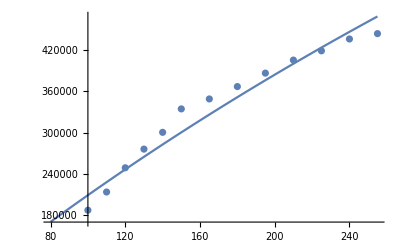

```mathematica
(* Plots mit maximalen Intensitäten - Temperatur *)
allmaxintplot={};
For[i=1,i≤Length[fits],i++,AppendTo[allmaxintplot,ampl/.fits[[i,2]]["BestFitParameters"]]]
allmaxintplot=Delete[allmaxintplot,{{15},{16}}];
allmaxintplot=Sort[allmaxintplot];
ListPlot[Transpose[{temperatures,allmaxintplot}]];

(* Plots mit integrierten Intensitäten - Temperatur *)
allintintplot = {};
For[i=1,i≤Length[fits],i++,AppendTo[allintintplot,Integrate[fits[[i,2]][x],{x,600,700}]]]
allintintplot=Delete[allintintplot,{{15},{16}}];
allintintplot=Sort[allintintplot];

intensityfit =NonlinearModelFit[Transpose[{temperatures,allintintplot}],I0/(1+a*Exp[-Ea1/( 8.617*10^-5*T)]),{I0,a,{Ea1,0.001}},T]


Show[Plot[intensityfit[T],{T,Min[temperatures],Max[temperatures]}],ListPlot[Transpose[{temperatures,allintintplot}]]]
```

```mathematica
intensityfit["BestFitParameters"]
```

{I0→3.10052,a→-0.999999,Ea1→1.16451×10^-7}

```mathematica
(* Plots mit Energie - Temperatur *)
allerrors = {};
For[i=1,i≤Length[fits],i++,AppendTo[allerrors,fits[[i,2]]["ParameterErrors"][[2]]]]
allerrors=Delete[allerrors,{{15},{16}}];
allerrors=Sort[allerrors]^2;
temporaer=Transpose[{Transpose[{temperatures,1240/allpeaksplot}],Map[ErrorBar,allerrors]}];
ErrorListPlot[{temporaer}];

(* Funktionen für geschätzte Zusammensetzung *)
Subscript[a, InP]=5.8687;
Subscript[a, GaP]=5.4505;
Subscript[a, GaAs]=5.65325;
Subscript[Eg, InP][T_]:=1.421 - 4.9*10^-4*T^2/(T+327);
Subscript[Eg, GaP][T_]:=2.34 - 6*10^-4*T^2/(T+460);
Clear[x];
x=First[x/.Solve[Subscript[a, GaAs]==x*Subscript[a, GaP]+(1-x)*Subscript[a, InP],x]];

(* Fit für Varshnigleichung + Test für Berechnung im Praktikum *)
nlm = NonlinearModelFit[Transpose[{temperatures,1240/allpeaksplot}],E0-α*T^2/(T+β),{E0,α,β},T,Weights->1/allerrors];
nlm["BestFitParameters"]
energtemp =Show[Plot[{nlm[T],x*Subscript[Eg, GaP][T]+(1-x)*Subscript[Eg, InP][T]},{T,Min[temperatures],Max[temperatures]},PlotRange->All,AxesLabel->{"T [K]","E_g [eV]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14],ImageSize->Large,AxesOrigin->{Min[temperatures],1.83}],ErrorListPlot[{temporaer}]];
Export["energtemp.eps",energtemp];
```

Part::partw: Part 2 of 615[ParameterErrors] does not exist.

Part::partw: Part 2 of 619[ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{80,90,100,110,120,130,140,150,165,180,195,210,225,240,255},1240/allpeaksplot} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[{{80,90,100,110,120,130,140,150,165,180,195,210,225,240,255},1240/allpeaksplot}],{ErrorBar[(615[ParameterErrors]⟦2⟧)^2],ErrorBar[(615[ParameterErrors]⟦2⟧)^2],ErrorBar[(618[ParameterErrors]⟦2⟧)^2],ErrorBar[(618[ParameterErrors]⟦2⟧)^2],ErrorBar[(619[ParameterErrors]⟦2⟧)^2],ErrorBar[(620[ParameterErrors]⟦2⟧)^2],ErrorBar[(620[ParameterErrors]⟦2⟧)^2],ErrorBar[(620[Para…rrors]⟦2⟧)^2],ErrorBar[(621[ParameterErrors]⟦2⟧)^2],ErrorBar[(622[ParameterErrors]⟦2⟧)^2],ErrorBar[(626[ParameterErrors]⟦2⟧)^2],ErrorBar[(626[ParameterErrors]⟦2⟧)^2],ErrorBar[(630[ParameterErrors]⟦2⟧)^2],ErrorBar[(631[ParameterErrors]⟦2⟧)^2],ErrorBar[(632[ParameterErrors]⟦2⟧)^2]}} cannot be transposed.

Transpose::nmtx: The first two levels of {{80,90,100,110,120,130,140,150,165,180,195,210,225,240,255},1240/allpeaksplot} cannot be transposed.

NonlinearModelFit::wts: The value of option Weights -> {1/(615[ParameterErrors]⟦2⟧)^2,1/(615[ParameterErrors]⟦2⟧)^2,1/(618[ParameterErrors]⟦2⟧)^2,1/(618[ParameterErrors]⟦2⟧)^2,1/(619[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(621[ParameterErrors]⟦2⟧)^2,1/(622[ParameterErrors]⟦2⟧)^2,1/(626[ParameterErrors]⟦2⟧)^2,1/(626[ParameterErrors]⟦2⟧)^2,1/(630[ParameterErrors]⟦2⟧)^2,1/(631[ParameterErrors]⟦2⟧)^2,1/(632[ParameterErrors]⟦2⟧)^2} should be a list of real numbers or a pure function.

NonlinearModelFit[Transpose[{{80,90,100,110,120,130,140,150,165,180,195,210,225,240,255},1240/allpeaksplot}],E0-(T^2 α)/(T+β),{E0,α,β},T,Weights→{1/(615[ParameterErrors]⟦2⟧)^2,1/(615[ParameterErrors]⟦2⟧)^2,1/(618[ParameterErrors]⟦2⟧)^2,1/(618[ParameterErrors]⟦2⟧)^2,1/(619[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(621[ParameterErrors]⟦2⟧)^2,1/(622[ParameterErrors]⟦2⟧)^2,1/(626[ParameterErrors]⟦2⟧)^2,1/(626[ParameterErrors]⟦2⟧)^2,1/(630[ParameterErrors]⟦2⟧)^2,1/(631[ParameterErrors]⟦2⟧)^2,1/(632[ParameterErrors]⟦2⟧)^2}]

NonlinearModelFit::wts: The value of option Weights -> {1/(615[ParameterErrors]⟦2⟧)^2,1/(615[ParameterErrors]⟦2⟧)^2,1/(618[ParameterErrors]⟦2⟧)^2,1/(618[ParameterErrors]⟦2⟧)^2,1/(619[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(621[ParameterErrors]⟦2⟧)^2,1/(622[ParameterErrors]⟦2⟧)^2,1/(626[ParameterErrors]⟦2⟧)^2,1/(626[ParameterErrors]⟦2⟧)^2,1/(630[ParameterErrors]⟦2⟧)^2,1/(631[ParameterErrors]⟦2⟧)^2,1/(632[ParameterErrors]⟦2⟧)^2} should be a list of real numbers or a pure function.

Transpose::nmtx: The first two levels of {{80.,90.,100.,110.,120.,130.,140.,150.,165.,180.,195.,210.,225.,240.,255.},1240./allpeaksplot} cannot be transposed.

Part::partw: Part 2 of 615.[ParameterErrors] does not exist.

Part::partw: Part 2 of 618.[ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {1/(615.[ParameterErrors]⟦2⟧)^2,1/(615.[ParameterErrors]⟦2⟧)^2,1/(618.[ParameterErrors]⟦2⟧)^2,1/(618.[ParameterErrors]⟦2⟧)^2,1/(619.[ParameterErrors]⟦2⟧)^2,1/(620.[ParameterErrors]⟦2⟧)^2,1/(620.[ParameterErrors]⟦2⟧)^2,1/(620.[ParameterErrors]⟦2⟧)^2,1/(621.[ParameterErrors]⟦2⟧)^2,1/(622.[ParameterErrors]⟦2⟧)^2,1/(626.[ParameterErrors]⟦2⟧)^2,1/(626.[ParameterErrors]⟦2⟧)^2,1/(630.[ParameterErrors]⟦2⟧)^2,1/(631.[ParameterErrors]⟦2⟧)^2,1/(632.[ParameterErrors]⟦2⟧)^2} should be a list of real numbers or a pure function.

NonlinearModelFit::wts: The value of option Weights -> {1/(615[ParameterErrors]⟦2⟧)^2,1/(615[ParameterErrors]⟦2⟧)^2,1/(618[ParameterErrors]⟦2⟧)^2,1/(618[ParameterErrors]⟦2⟧)^2,1/(619[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(620[ParameterErrors]⟦2⟧)^2,1/(621[ParameterErrors]⟦2⟧)^2,1/(622[ParameterErrors]⟦2⟧)^2,1/(626[ParameterErrors]⟦2⟧)^2,1/(626[ParameterErrors]⟦2⟧)^2,1/(630[ParameterErrors]⟦2⟧)^2,1/(631[ParameterErrors]⟦2⟧)^2,1/(632[ParameterErrors]⟦2⟧)^2} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{80.,90.,100.,110.,120.,130.,140.,150.,165.,180.,195.,210.,225.,240.,255.},1240./allpeaksplot} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ErrorListPlot[{Transpose[{Transpose[{{«15»},Times[«2»]}],{ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]],ErrorBar[Power[«2»]]}}]}]].